I have used U = ⅇ^(ⅈ H t).  I need to go back and flip the sign of t.

There are also some that have Conjugate[Transpose[ψ]]ⅇ^(ⅈ e dt)ψ instead of Transpose[ψ]ⅇ^(ⅈ e dt)Conjugate[ψ]

## From the initial Hamiltonian

```mathematica
H[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];

htp = 1/2 ω1 Z1+1/2 ω2 Z2+1/2 ω3 Z3+Ω1 Cos[ωr1 t +ϕ1] X1+Ω2 Cos[ωr2 t +ϕ2]X2+Ω3 Cos[ωr3 t +ϕ3]X3+1/2 ω12 X1.X2+1/2 ω23 X2.X3+1/2 ω31 X3.X1+Λ X1.X2.X3;

htp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=6;
Λ=0.01;
h=H[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
```

```mathematica
U[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=H[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Conjugate[Transpose[ψt]].DiagonalMatrix[ⅇ^(ⅈ et dt)].ψt;

utp
];
```

```mathematica
ψT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ti,ut,ht,et,ψt},
ψtp=ψ0;
For[ti=dt,ti≤t,ti+=dt,
ut =U[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ψtp
];
```

```mathematica
ψ000=Table[0,{i,1,8}];
ψ000[[1]]=1;
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=6;
Λ=0.01;
dt = 0.01;
ψt = ψT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
```

```mathematica
ψt
```

{0.140547-0.284268 ⅈ,-0.024367+0.139851 ⅈ,0.0103932+0.534371 ⅈ,0.0485667+0.0955681 ⅈ,0.304843-0.0434508 ⅈ,-0.0360516+0.0272805 ⅈ,0.305219+0.605713 ⅈ,0.157459+0.0208106 ⅈ}

## After first rotation, before rotating wave approximation

```mathematica
Ha[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];

h1=1/2(ω1-ωr1) Z1+Ω1 Cos[ωr1 t +ϕ1]( Cos[t ωr1+ϕ1]I0[3]+ⅈ Sin[t ωr1+ϕ1]Z1).X1;
h2=1/2(ω2-ωr2) Z2+Ω2 Cos[ωr2 t +ϕ2]( Cos[t ωr2+ϕ2]I0[3]+ⅈ Sin[t ωr2+ϕ2]Z2).X2;
h3=1/2(ω3-ωr3) Z3+Ω3 Cos[ωr3 t +ϕ3]( Cos[t ωr3+ϕ3]I0[3]+ⅈ Sin[t ωr3+ϕ3]Z3).X3 ;
h12=1/2 ω12 ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2);
h23=1/2 ω23 ( Cos[t ωr2+ϕ2]X2- Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3-Sin[t ωr3+ϕ3]Y3);
h31=1/2 ω31 ( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3).( Cos[t ωr1+ϕ1]X1-Sin[t ωr1+ϕ1]Y1);
h123=Λ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3);

htp = h1+h2+h3+h12+h23+h31+h123;

htp
];
```

```mathematica
Ra[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{rtp,ua,uc,ud,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);

ua = (Cos[(ωr1 t+ϕ1)/2]I0[3]-ⅈ Sin[(ωr1 t +ϕ1)/2]Z1).(Cos[(ωr2 t+ϕ2)/2]I0[3]-ⅈ Sin[(ωr2 t +ϕ2)/2]Z2).(Cos[(ωr3 t+ϕ3)/2]I0[3]-ⅈ Sin[(ωr3 t +ϕ3)/2]Z3);


rtp = ua;


rtp
];
```

```mathematica
RdRa[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{rtp,ua,uc,ud,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);

ua =-ⅈ ωr1/2 Z1-ⅈ ωr2/2 Z2-ⅈ ωr3/2 Z3;

rtp = ua;


rtp
];
```

```mathematica
Ua[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Ha[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Conjugate[Transpose[ψt]].DiagonalMatrix[ⅇ^(ⅈ et dt)].ψt;

utp
];
```

```mathematica
ψaT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ra,ti,ut,ht,et,ψt},
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0];
ψtp=ψ0;
ψtp=ra.ψtp;
For[ti=dt,ti≤t,ti+=dt,
ut =Ua[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
ψtp=Conjugate[Transpose[ra]].ψtp;
ψtp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
h=H[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
ha=Ha[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
```

```mathematica
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
rdr =RdRa[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
```

```mathematica
Max[Abs[ha-Conjugate[Transpose[ra]].h.ra+ⅈ rdr]]
```

7.85046×10^-17

```mathematica
ψ000=Table[0,{i,1,8}];
ψ000[[1]]=1;
dt=0.001;
ψt = ψT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
ψat = ψaT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
```

```mathematica
ψt-ψat
```

{-3.55554×10^-9+9.7231×10^-9 ⅈ,2.86012×10^-6+2.06442×10^-6 ⅈ,0.0000493724+0.0000119013 ⅈ,0.0000114699+3.05269×10^-6 ⅈ,0.0000271279+7.26178×10^-6 ⅈ,5.38651×10^-6+2.25348×10^-6 ⅈ,0.0000143117+0.0000168434 ⅈ,2.57411×10^-6+5.30369×10^-6 ⅈ}

## After the rotating wave approximation

```mathematica
Haeff[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];

h1=1/2(ω1-ωr1) Z1+1/2 Ω1 X1;
h2=1/2(ω2-ωr2) Z2+1/2 Ω2 X2;
h3=1/2(ω3-ωr3) Z3+1/2 Ω3 X3 ;
h12=1/2 ω12 ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2);
h23=1/2 ω23 ( Cos[t ωr2+ϕ2]X2- Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3-Sin[t ωr3+ϕ3]Y3);
h31=1/2 ω31 ( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3).( Cos[t ωr1+ϕ1]X1-Sin[t ωr1+ϕ1]Y1);
h123=Λ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3);

htp = h1+h2+h3+h12+h23+h31+h123;

htp
];
```

```mathematica
Uaeff[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Haeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(ⅈ et dt)].Conjugate[ψt];

utp
];
```

```mathematica
ψaeffT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ra,ti,ut,ht,et,ψt},
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0];
ψtp=ψ0;
ψtp=ra.ψtp;
For[ti=dt,ti≤t,ti+=dt,
ut =Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
ψtp=Conjugate[Transpose[ra]].ψtp;
ψtp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
(*This part is highly unoptimized*)
ψ000=Table[0,{i,1,8}];
ψ000[[1]]=1;
dt=0.001;
ovrl={{0,Re[Conjugate[ψ000].ψ000]}};
ovil={{0,Im[Conjugate[ψ000].ψ000]}};
For[t=dt,t≤0.5,t+=dt,
ψt = ψT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
ψat = ψaT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
ov=Conjugate[ψt].ψat;
ovrl=Join[ovrl,{{t,Re[ov]}}];
ovil=Join[ovil,{{t,Im[ov]}}];
If[Chop[Mod[t,0.1]]==0,Print[{t,ov}]]
];
```

{0.1,1.+7.93762×10^-7 ⅈ}

{0.2,1.+2.99927×10^-6 ⅈ}

{0.3,1.+6.34542×10^-6 ⅈ}

{0.4,1.+0.0000105698 ⅈ}

{0.5,1.+0.0000154261 ⅈ}

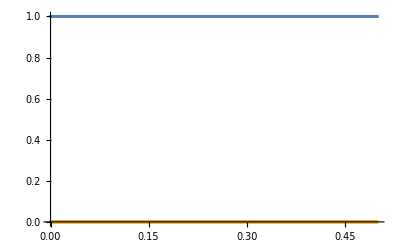

```mathematica
ListPlot[{ovrl,ovil}]
```

## After second rotation

```mathematica
Hc[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);


h12=1/2 ω12( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1)).( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2));
h23=1/2 ω23 ( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3));
h31=1/2 ω31 ( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3)).( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1));

h123=Λ ( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- Sin[ζ1]( Cos[η1 t]I0[3].Z1+ Sin[η1 t]Y1))- Sin[t ωr1+ϕ1]( Cos[η1 t]Y1- Sin[η1 t]Z1)).( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- Sin[ζ2]( Cos[η2 t]Z2+Sin[η2 t]Y2))-Sin[t ωr2+ϕ2]( Cos[η2 t]Y2- Sin[η2 t]Z2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- Sin[ζ3]( Cos[η3 t]Z3+ Sin[η3 t]Y3))- Sin[t ωr3+ϕ3]( Cos[η3 t]Y3-Sin[η3 t]Z3));

htp =h12+h23+h31+h123;

htp
];
```

```mathematica
Uc[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Hc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Conjugate[Transpose[ψt]].DiagonalMatrix[ⅇ^(ⅈ et dt)].ψt;

utp
];
```

```mathematica
Rc[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{rtp,ua,uc,ud,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);


uc=(Cos[ζ1/2]I0[3]+ⅈ Sin[ζ1/2]Y1).(Cos[ζ2/2]I0[3]+ⅈ Sin[ζ2/2]Y2).(Cos[ζ3/2]I0[3]+ⅈ Sin[ζ3/2]Y3);

ud=(Cos[η1/2 t]I0[3]-ⅈ Sin[η1/2 t]X1).(Cos[η2/2 t]I0[3]-ⅈ Sin[η2/2 t]X2).(Cos[η3/2 t]I0[3]-ⅈ Sin[η3/2 t]X3);

rtp = uc.ud;


rtp
];
```

```mathematica
RdRc[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{rtp,ua,uc,ud,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);


rtp = -ⅈ 1/2 η1 X1-ⅈ 1/2 η2 X2-ⅈ 1/2 η3 X3;


rtp
];
```

```mathematica
Uc[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Hc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(ⅈ et dt)].Conjugate[ψt];

utp
];
```

```mathematica
ψcT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ra,ti,ut,ht,et,ψt},
ra=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0];
ψtp=ψ0;
ψtp=ra.ψtp;
For[ti=dt,ti≤t,ti+=dt,
ut =Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ra=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
ψtp=Conjugate[Transpose[ra]].ψtp;
ψtp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;

haeff=Haeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
hc=Hc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];

rc=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
rdrc =RdRc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];

Max[Abs[hc-Conjugate[Transpose[rc]].haeff.rc+ⅈ rdrc]]
```

2.22478×10^-16

```mathematica
Max[Abs[rc.hc.rcc +ⅈ rc.rdrc.rcc -haeff]]
```

1.11239×10^-16

```mathematica
rc=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
rcc=Conjugate[Transpose[rc]];
rc1=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t-dt];
rcc1=Conjugate[Transpose[rc1]];

uc =Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
```

```mathematica
Max[Abs[Chop[rc1.MatrixExp[ⅈ (hc)dt].rcc-rc1.uc.rcc]]]
```

0

```mathematica
Max[Abs[Chop[rc.(I0[3]-rcc.( rc-rc1)).MatrixExp[ⅈ (hc)dt].rcc-rc1.uc.rcc]]]
```

0

```mathematica
Max[Abs[Chop[rc.(I0[3]- rdrc dt).MatrixExp[ⅈ (hc)dt].rcc-rc1.uc.rcc]]]
```

9.27054×10^-8

```mathematica
Max[Abs[Chop[(I0[3]- rc.rdrc.rcc dt).rc.MatrixExp[ⅈ (hc)dt].rcc-rc1.uc.rcc]]]
```

9.27054×10^-8

```mathematica
Max[Abs[Chop[(I0[3]- rc.rdrc.rcc dt).MatrixExp[ⅈ (rc.hc.rcc )dt]-rc1.uc.rcc]]]
```

9.27054×10^-8

```mathematica
Max[Abs[Chop[MatrixExp[ⅈ (rc.hc.rcc +ⅈ rc.rdrc.rcc )dt]-rc1.uc.rcc]]]
```

2.49167×10^-8

```mathematica
Max[Abs[Chop[MatrixExp[ⅈ (haeff)dt]-rc1.uc.rcc]]]
```

2.49167×10^-8

```mathematica
dt=0.001;
Max[Abs[rc1.Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt].rcc-Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt]]]
```

2.49167×10^-8

```mathematica
dt=0.001;
Max[Abs[Conjugate[Transpose[rc1.Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt].rcc]]-Conjugate[Transpose[Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt]]]]]
```

2.49167×10^-8

```mathematica
dt=0.001;
Max[Abs[rc.Conjugate[Transpose[Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt]]].rcc1-Conjugate[Transpose[Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt]]]]]
```

2.49167×10^-8

```mathematica
ht=Hc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
uc =Transpose[ψt].DiagonalMatrix[ⅇ^(ⅈ et dt)].Conjugate[ψt];

Max[Abs[Conjugate[Transpose[Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt]]]-Transpose[ψt].DiagonalMatrix[ⅇ^(-ⅈ et dt)].Conjugate[ψt]]]
```

1.81608×10^-16

```mathematica
ψ000=Table[0,{i,1,8}];
ψ000[[1]]=1;
dt=0.001;
ψaefft = ψaeffT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
ψct = ψcT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
```

```mathematica
ψct
ψaefft
```

{0.978448-0.00367512 ⅈ,-0.00144192+0.0205411 ⅈ,0.0116818+0.172319 ⅈ,0.00386391-0.0174794 ⅈ,-0.00109213+0.0966152 ⅈ,-0.00841718-0.0142352 ⅈ,-0.0485225+0.00490948 ⅈ,0.00646163-0.00468337 ⅈ}

{0.935105+0.28856 ⅈ,-0.0000344808+0.00812186 ⅈ,0.126227+0.113435 ⅈ,-0.00333652+0.0258516 ⅈ,0.00338034+0.0971765 ⅈ,-0.00385811+0.0172922 ⅈ,-0.0112681+0.0527388 ⅈ,-0.00439917+0.00829351 ⅈ}